{c→1.68619,b→1.19418}

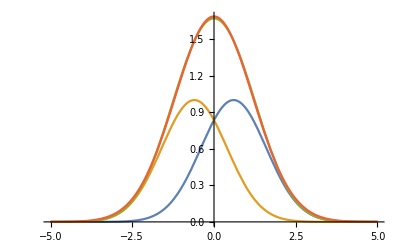

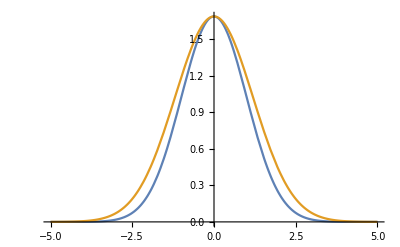

```mathematica
w=1;
f[x_,w_]:=Exp[-x^2/(2 w^2)]
a = 0.6;
data=Table[{i, f[i-a w,w]+f[i+a w,w]},{i,-3,3,0.1}];
sol=FindFit[data,c f[x,b],{c,b},x]
Plot[{f[x-a w,w],f[x+a w,w], f[x-a w,w]+f[x+a w,w],c f[x,b]/.sol},{x,-5,5}]
Plot[{c f[x,w]/.sol,c f[x,b]/.sol},{x,-5,5}]
```